```mathematica
A[n_]:=(-1)^(n+1)
```

```mathematica
Table[A[n],{n,1,20}]
```

{1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1}

```mathematica
S[n_]:=Sum[A[k],{k,1,n}]
```

```mathematica
Table[S[n],{n,1,20}]
```

{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}

```mathematica
Sum[A[n],{n,1,Infinity}]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ (-1)^(1+n)

```mathematica
T[n_]:=(1/n) Sum[S[k],{k,1,n}]
```

```mathematica
Table[T[n],{n,1,20}]
```

{1,1/2,2/3,1/2,3/5,1/2,4/7,1/2,5/9,1/2,6/11,1/2,7/13,1/2,8/15,1/2,9/17,1/2,10/19,1/2}

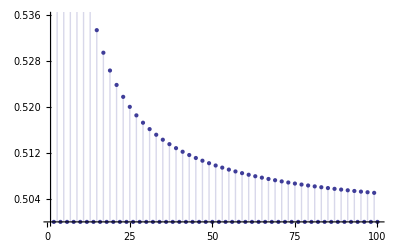

```mathematica
DiscretePlot[T[n],{n,1,100}]
```

```mathematica
Limit[T[n],{n->Infinity}]
```

{1/2}

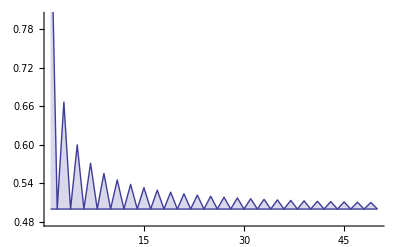

```mathematica
Show[Plot[1/2,{x,1,50},PlotRange->{.48,.8}],DiscretePlot[T[n],{n,1,50},Joined->True]]
```